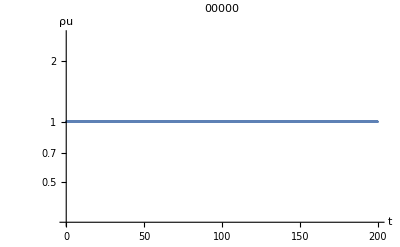

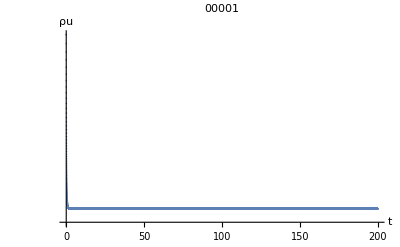

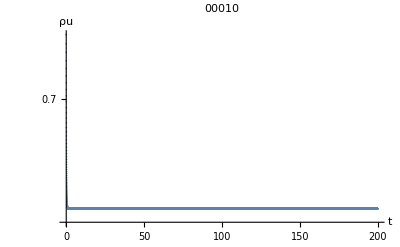

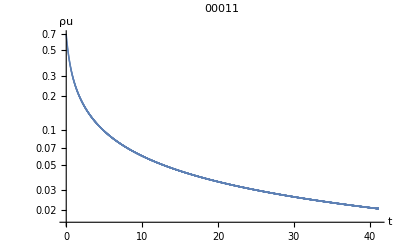

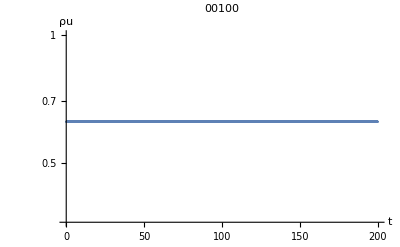

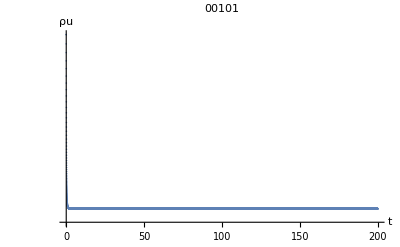

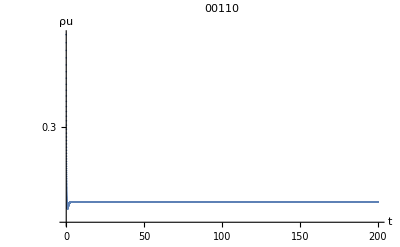

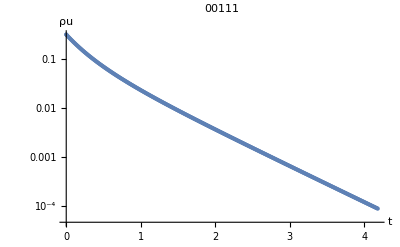

```mathematica
rules = {"00000","00001","00010","00011","00100","00101","00110","00111","01000","01001","01010","01011","01100","01101","01110","01111","10000","10001","10010","10011","10100","10101","10110","10111","11000","11001","11010","11011","11100","11101","11110","11111"};
data = {};
Do[AppendTo[data, Import["/home/vynie/Documents/PycharmProjects/gameoflife/Output/ScriptOutput/S0/"<>rules[[i]]<>"_s0.csv", HeaderLines->1]];
data[[i]] = data[[i]][[All, {1, 2}]];
Print[ListLogPlot[data[[i]],  PlotRange->All, PlotLabel->rules[[i]], AxesLabel->{"t", "ρu"}]]
, {i, 1, 31}];
```